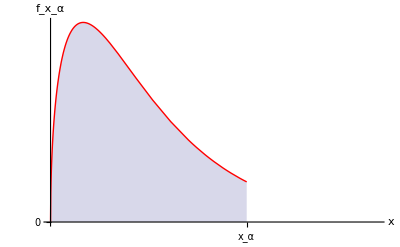

```mathematica
Needs["PlotLegends`"];
Ct=Evaluate@Table[PDF[ChiSquareDistribution[q],x],{q,{3}}];
figure=Plot[
{Ct},
{x,0,10},
PlotPoints->20,
PlotStyle->{Red},
Ticks->{ { {6,Subscript[x, α],{0.2,0}} } ,{0}},
Filling->Axis,
AxesLabel->{x,Subscript[f, Subscript[x, α]]},
RegionFunction->Function[{x,y},Abs[x]<6],
PlotLegend->{χ^2 (N-q)},
LegendSize->{0.55,0.15},
LegendPosition->{0.3,0.2},
LegendShadow->{0,0}
]
Export["/home/federico/workspace/books/imadls/mathematica/chiquadrotest.eps",figure,"EPS"];
```